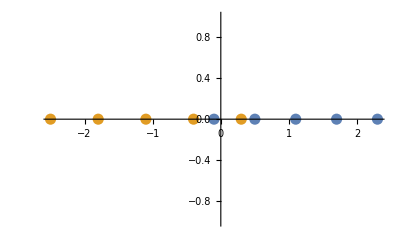

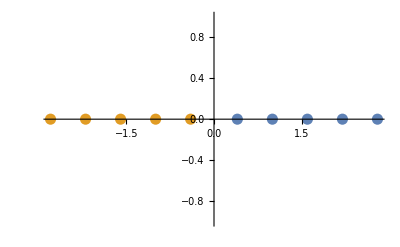

```mathematica
points1Sep=Table[{0.6*i-0.2,0},{i,5}]; (*belongs on the right side *)
points2Sep=Table[{-0.6*i+0.2,0},{i,5}]; (*belongs on the left side *)
points1=Table[{0.6*i-0.7,0},{i,5}];
points2=Table[{-0.7*i+1.0,0},{i,5}]; 
ListPlot[{points1, points2},PlotStyle->PointSize[0.02]]
ListPlot[{points1Sep, points2Sep},PlotStyle->PointSize[0.02]]
```

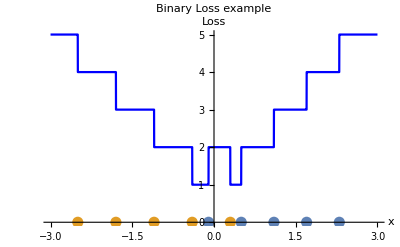

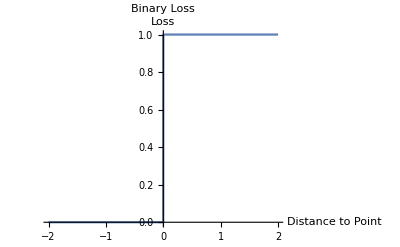

```mathematica
lossName="Binary Loss";
binLoss[x_,p_,class_]:=If[class==1,If[p>x,0,1],If[p<x,0,1]];
applyLossForPlt[x_,points_,class_,lossFKT_]:=Total[Map[Function[p,lossFKT[x,p[[1]],class]],points]];
Show[Plot[{applyLossForPlt[x,points1,1,binLoss]+applyLossForPlt[x,points2,2,binLoss],0},{x,-3,3},PlotStyle->{Blue,White}, Exclusions->None, PlotLabel->lossName<>" example",AxesLabel->{x,Loss}],ListPlot[{points1, points2},PlotStyle->PointSize[0.02]]]
Plot[binLoss[x,0,1],{x,-2,2},PlotLabel->lossName,AxesLabel->{"Distance to Point",Loss}]
```

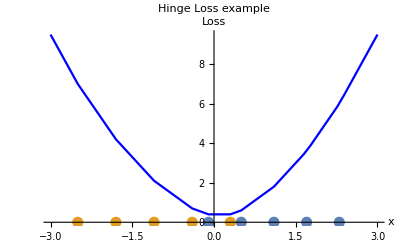

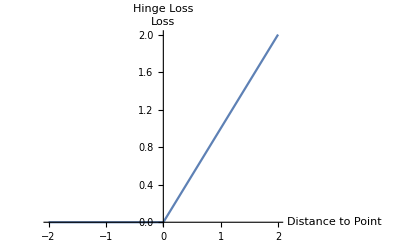

```mathematica
hingeLoss[x_,p_,class_]:=If[class==1,Max[0,x-p],Max[0,p-x]];
lossName="Hinge Loss";
Show[Plot[{applyLossForPlt[x,points1,1,hingeLoss]+applyLossForPlt[x,points2,2,hingeLoss],0},{x,-3,3},PlotStyle->{Blue,White}, Exclusions->None, PlotLabel->lossName<>" example",AxesLabel->{x,Loss}],ListPlot[{points1, points2},PlotStyle->PointSize[0.02]]]
Plot[hingeLoss[x,0,1],{x,-2,2},PlotLabel->lossName,AxesLabel->{"Distance to Point",Loss}]
```

C:\Users\Hendrik\Dropbox\ML-Presentation

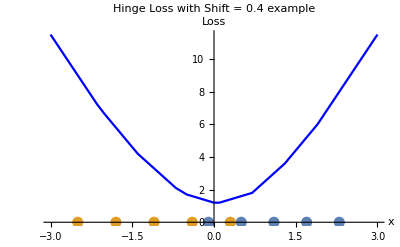

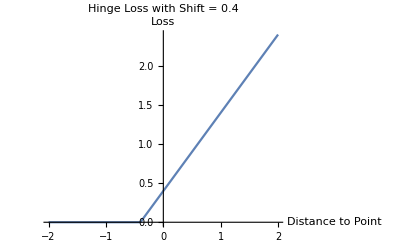

```mathematica
hingeLossShift[shift_]:=Function[{x,p,class},If[class==1,Max[0,x-p+shift],Max[0,p-x+shift]]];
sft=0.4;
lossName="Hinge Loss with Shift = " <>ToString[sft];
SetDirectory[NotebookDirectory[]]
Show[Plot[{applyLossForPlt[x,points1,1,hingeLossShift[sft]]+applyLossForPlt[x,points2,2,hingeLossShift[sft]] ,0},{x,-3,3},PlotStyle->{Blue,White},Exclusions->None, PlotLabel->lossName<>" example",AxesLabel->{x,Loss}],ListPlot[{points1, points2},PlotStyle->PointSize[0.02]]]
Plot[hingeLossShift[sft][x,0,1],{x,-2,2},PlotLabel->lossName,AxesLabel->{"Distance to Point",Loss}]
```

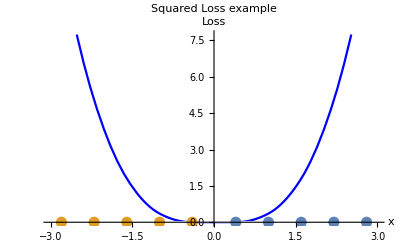

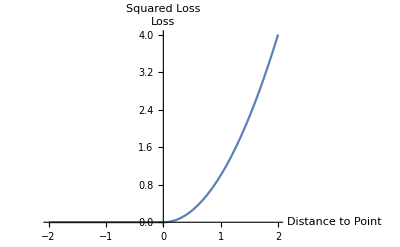

```mathematica
mseLoss[x_,p_,class_]:=If[class==1,(Max[0,x-p])^2,(Max[0,p-x])^2];
lossName="Squared Loss";
Show[Plot[{applyLossForPlt[x,points1,1,mseLoss]+applyLossForPlt[x,points2,2,mseLoss],0},{x,-3,3},PlotStyle->{Blue,White}, Exclusions->None, PlotLabel->lossName<>" example",AxesLabel->{x,Loss}],ListPlot[{points1, points2},PlotStyle->PointSize[0.02]]]
Plot[mseLoss[x,0,1],{x,-2,2},PlotLabel->lossName,AxesLabel->{"Distance to Point",Loss}]
```

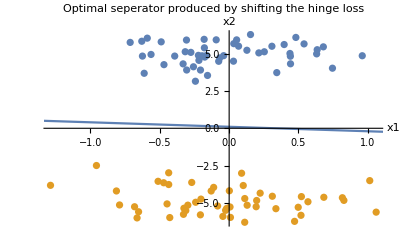

```mathematica
SeedRandom[45];
numsToGenerate=50;
spread = 0.4;
points1SVM=Table[{RandomVariate[NormalDistribution[0,spread]],RandomVariate[NormalDistribution[5.0,spread*2]]},{i,numsToGenerate}] ;(*belongs on the upper quadrant side *)
points2SVM=Table[{RandomVariate[NormalDistribution[0,spread]],RandomVariate[NormalDistribution[-5.0,spread*2]]},{i,numsToGenerate}] ;(*belongs on the lower quadrant side *)
outlieres1 = {{0.1,0.3}} ;
outlieres2 = {{-0.1,-0.3},{0.1,-0.8}};

Show[ListPlot[{points1SVM,points2SVM},PlotRange->All,PlotLabel->"Optimal seperator produced by shifting the hinge loss",AxesLabel->{x1,x2},PlotStyle->PointSize[0.013]],Plot[{-0.3*x+0.1},{x,-3.5,3},Evaluated->True]]
```